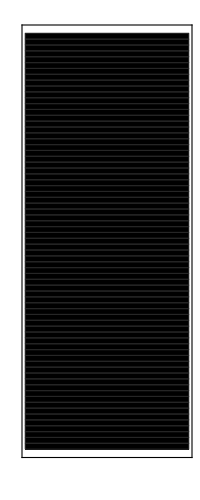
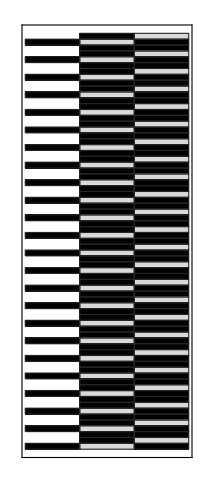
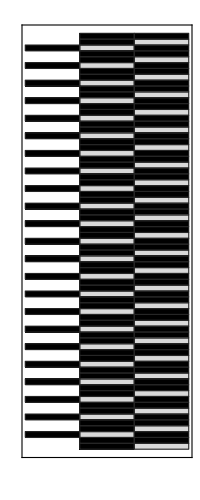
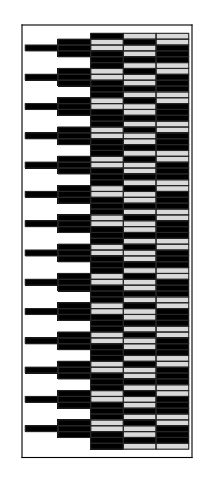
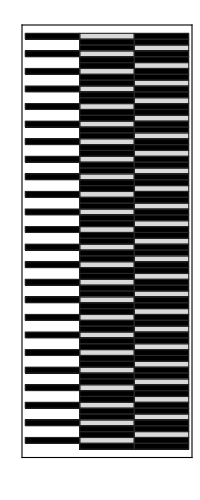
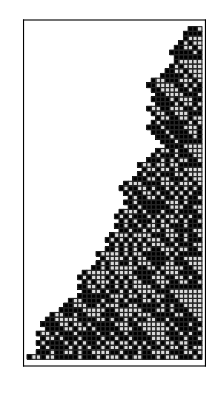
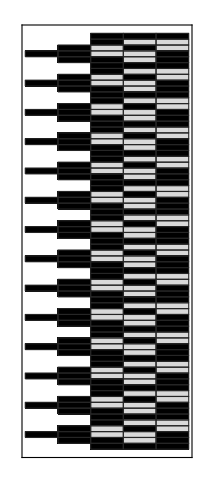
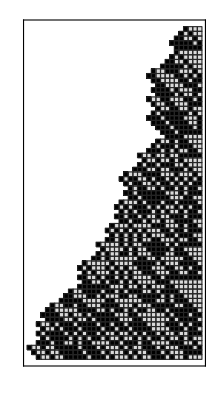

```mathematica
Table[ResourceFunction["RaggedDigitsPlot"][IntegerDigits[#,2]&/@NestList[If[EvenQ[#],(5 #)/2,(#+1)/2]&,n,70],],{n,1,10}]
```